```mathematica
Subscript[k, max]=30
Δt=0.01
```

30

0.01

```mathematica
lst=Table[(2 RandomReal[]-1)/(3 Mod[i,Subscript[k, max]+1]+1),{i,1,2 Subscript[k, max]+1}];
lst[[Subscript[k, max]+1]]=0;
u=Total[Table[lst⟦i⟧ Sin[i x],{i,1,Subscript[k, max]}]]+Total[Table[lst⟦i+Subscript[k, max]+1⟧ Cos[i x],{i,0,Subscript[k, max]}]];
u0=u;
unew=Total[Table[Subscript[a, i] Sin[i x],{i,1,Subscript[k, max]}]]+Total[Table[Subscript[a, i+Subscript[k, max]+1] Cos[i x],{i,0,Subscript[k, max]}]];
```

```mathematica
ν=0.1;
solution={};
Monitor[For[t=0,t<1,t+=Δt,u=Total[Table[lst⟦i⟧ Sin[i x],{i,1,Subscript[k, max]}]]+Total[Table[lst⟦i+Subscript[k, max]+1⟧ Cos[i x],{i,0,Subscript[k, max]}]];equations=Table[(unew==u+(ν D[u, {x,2}]-u D[u, x]) Δt)/.x->(2 π i)/Length[lst],{i,1,Length[lst]}];
lst=Table[Subscript[a, i],{i,1,Length[lst]}]/.FindRoot[equations,Table[{Subscript[a, i],lst[[i]]},{i,1,Length[lst]}]];solution=Append[solution,lst]],t]
```

```mathematica
Manipulate[u=Total[Table[solution[[j]]⟦i⟧ Sin[i x],{i,1,Subscript[k, max]}]]+Total[Table[solution[[j]]⟦i+Subscript[k, max]+1⟧ Cos[i x],{i,0,Subscript[k, max]}]];
Plot[u/.x->y,{y,0,2 π},PlotRange->{{0,2*π},{-0.3,0.3}}],{j,1,Length[solution],1}]
```

```mathematica
Clear[t,v]
sol=NDSolveValue[{ν D[v[x,t], {x,2}]-v[x,t] D[v[x,t], x]==D[v[x,t], t],v[0,t]==v[2 π,t],v[x,0]==u0},v,{x,0,1},{t,0,1}]
```

InterpolatingFunction[…]

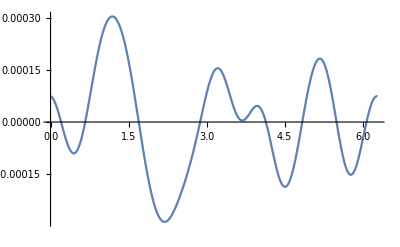

```mathematica
Plot[sol[y,1]-u/.x->y,{y,0,2 π}]
```